```mathematica
<<MaTeX`
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
folder="D:\\Documents\\PKU-PHY\\__研究生\\__工作\\生物磁源定位\\_myMNE\\v5-流程规范\\figs\\regularized-deadzone\\intrisicNoise-z";
data3sd=Import[folder<>"\\results-3s-d.csv"]//Transpose;
data3sn=Import[folder<>"\\results-3s-n.csv"]//Transpose;
data3vn=Import[folder<>"\\results-3v-n.csv"]//Transpose;
```

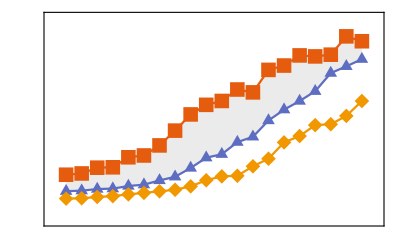

```mathematica
ListLinePlot[{data3sd[[;;,1;;2]],data3sn[[;;,1;;2]],data3vn[[;;,1;;2]]},PlotMarkers->{{"■",15},{"▲",15},{"◆",15}},PlotStyle->colors,Filling->{1->{2}},FillingStyle->Directive[LightGray,Opacity[0.5]],PlotTheme->"Scientific",GridLines->None,FrameTicks->None,PlotRange->{{0,2.1*10^(-13)},{0,0.05}}]
```

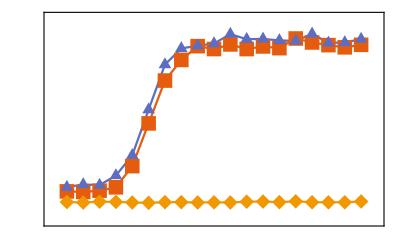

```mathematica
folder="D:\\Documents\\PKU-PHY\\__研究生\\__工作\\生物磁源定位\\_myMNE\\v5-流程规范\\figs\\regularized-deadzone\\axisAngleError";
data3sRx=Import[folder<>"\\results-3sRx.csv"]//Transpose;
data3sRz=Import[folder<>"\\results-3sRz.csv"]//Transpose;
data3v=Import[folder<>"\\results-3v.csv"]//Transpose;
ListLinePlot[{data3sRz[[;;,1;;2]],data3sRx[[;;,1;;2]],data3v[[;;,1;;2]]},PlotMarkers->{{"■",15},{"▲",15},{"◆",15}},PlotStyle->colors,PlotTheme->"Scientific",GridLines->None,FrameTicks->None,PlotRange->{{-5,95},{0,0.1}}]
```